```mathematica
SetDirectory[NotebookDirectory[]]
<<"milp_gen.wl"
<<"trivium.wl"
```

/Users/marco/marco.live/DIDATTICA/CORSI/2023-2024/IN450/code/IN450-2023/progetti/quintavalle

```mathematica
nround=3;
sols=GenerateTriviumMILP[nround]
key=Table[RandomInteger[{0,1}],80];
IV=Table[RandomInteger[{0,1}],80]
x=TriviumSetup[key,IV];
```

{{(u^0)_0,(u^0)_1,(u^0)_2,(u^0)_3,(u^0)_4,(u^0)_5,(u^0)_6,(u^0)_7,(u^0)_8,(u^0)_9,(u^0)_10,(u^0)_11,(u^0)_12,(u^0)_13,(u^0)_14,(u^0)_15,(u^0)_16,(u^0)_17,(u^0)_18,(u^0)_19,(u^0)_20,(u^0)_21,(u^0)_22,(u^0)_23,(u^0)_24,(u^0)_25,(u^0)_26,(u^0)_27,(u^0)_28,(u^0)_29,(u^0)_30,(u^0)_31,(u^0)_32,(u^0)_33,(u^0)_34,(u^0)_35,(u^0)_36,(u^0)_37,(u^0)_38,(u^0)_39,(u^0)_40,(u^0)_41,(u^0)_42,(u^0)_43,(u^0)_44,(u^0)_45,(u^0)_46,(u^0)_47,(u^0)_48,(u^0)_49,(u^0)_50,(u^0)_51,(u^0)_52,(u^0)_53,(u^0)_54,(u^0)_55,(u^0)_56,(u^0)_57,(u^0)_58,(u^0)_59,(u^0)_60,(u^0)_61,(u^0)_62,(u^0)_63,(u^0)_64,(u^0)_65,(u^0)_66,(u^0)_67,(u^0)_68,(u^0)_69,(u^0)_70,(u^0)_71,(u^0)_72,(u^0)_73,(u^0)_74,(u^0)_75,(u^0)_76,(u^0)_77,(u^0)_78,(u^0)_79,(v^0)_0,(v^0)_1,(v^0)_2,(v^0)_3,(v^0)_4,(v^0)_5,(v^0)_6,(v^0)_7,(v^0)_8,(v^0)_9,(v^0)_10,(v^0)_11,(v^0)_12,(v^0)_13,(v^0)_14,(v^0)_15,(v^0)_16,(v^0)_17,(v^0)_18,(v^0)_19,(v^0)_20,(v^0)_21,(v^0)_22,(v^0)_23,(v^0)_24,(v^0)_25,(v^0)_26,(v^0)_27,(v^0)_28,(v^0)_29,(v^0)_30,(v^0)_31,(v^0)_32,(v^0)_33,(v^0)_34,(v^0)_35,(v^0)_36,(v^0)_37,(v^0)_38,(v^0)_39,(v^0)_40,(v^0)_41,(v^0)_42,(v^0)_43,(v^0)_44,(v^0)_45,(v^0)_46,(v^0)_47,(v^0)_48,(v^0)_49,(v^0)_50,(v^0)_51,(v^0)_52,(v^0)_53,(v^0)_54,(v^0)_55,(v^0)_56,(v^0)_57,(v^0)_58,(v^0)_59,(v^0)_60,(v^0)_61,(v^0)_62,(v^0)_63,(v^0)_64,(v^0)_65,(v^0)_66,(v^0)_67,(v^0)_68,(v^0)_69,(v^0)_70,(v^0)_71,(v^0)_72,(v^0)_73,(v^0)_74,(v^0)_75,(v^0)_76,(v^0)_77,(v^0)_78,(v^0)_79,(v^0)_80,(v^0)_81,(v^0)_82,(v^0)_83,(v^0)_84,(v^0)_85,(v^0)_86,(v^0)_87,(v^0)_88,(v^0)_89,(v^0)_90,(v^0)_91,(v^0)_92,(v^0)_93,(v^0)_94,(v^0)_95,(v^0)_96,(v^0)_97,(v^0)_98,(v^0)_99,(v^0)_100,(v^0)_101,(v^0)_102,(v^0)_103,(v^0)_104,(v^0)_105,(v^0)_106,(v^0)_107,(v^0)_108,(v^0)_109,(v^0)_110,(v^0)_111,(v^0)_112,(v^0)_113,(v^0)_114,(v^0)_115,(v^0)_116,(v^0)_117,(v^0)_118,(v^0)_119,(v^0)_120,(v^0)_121,(v^0)_122,(v^0)_123,(v^0)_124,(v^0)_125,(v^0)_126,(v^0)_127,(v^0)_128,(v^0)_129,(v^0)_130,(v^0)_131,(v^0)_132,(v^0)_133,(v^0)_134,(v^0)_135,(v^0)_136,(v^0)_137,(v^0)_138,(v^0)_139,(v^0)_140,(v^0)_141,(v^0)_142,(v^0)_143,(v^0)_144,(v^0)_145,(v^0)_146,(v^0)_147,(v^0)_148,(v^0)_149,(v^0)_150,(v^0)_151,(v^0)_152,(v^0)_153,(v^0)_154,(v^0)_155,(v^0)_156,(v^0)_157,(v^0)_158,(v^0)_159,(v^0)_160,(v^0)_161,(v^0)_162,(v^0)_163,(v^0)_164,(v^0)_165,(v^0)_166,(v^0)_167,(v^0)_168,(v^0)_169,(v^0)_170,(v^0)_171,(v^0)_172,(v^0)_173,(v^0)_174,(v^0)_175,(v^0)_176,(v^0)_177,(v^0)_178,(v^0)_179,(v^0)_180,(v^0)_181,(v^0)_182,(v^0)_183,(v^0)_184,(v^0)_185,(v^0)_186,(v^0)_187,(v^0)_188,(v^0)_189,(v^0)_190,(v^0)_191,(v^0)_192,(v^0)_193,(v^0)_194,(v^0)_195,(v^0)_196,(v^0)_197,(v^0)_198,(v^0)_199,(v^0)_200,(v^0)_201,(v^0)_202,(v^0)_203,(v^0)_204,(v^0)_205,(v^0)_206,(v^0)_207,(v^0)_208,(v^0)_209,(v^0)_210,(v^0)_211,(v^0)_212,(v^0)_213,(v^0)_214,(v^0)_215,(v^0)_216,(v^0)_217,(v^0)_218,(v^0)_219,(v^0)_220,(v^0)_221,(v^0)_222,(v^0)_223,(v^0)_224,(v^0)_225,(v^0)_226,(v^0)_227,(v^0)_228,(v^0)_229,(v^0)_230,(v^0)_231,(v^0)_232,(v^0)_233,(v^0)_234,(v^0)_235,(v^0)_236,(v^0)_237,(v^0)_238,(v^0)_239,(v^0)_240,(v^0)_241,(v^0)_242,(v^0)_243,(v^0)_244,(v^0)_245,(v^0)_246,(v^0)_247,(v^0)_248,(v^0)_249,(v^0)_250,(v^0)_251,(v^0)_252,(v^0)_253,(v^0)_254,(v^0)_255,(v^0)_256,(v^0)_257,(v^0)_258,(v^0)_259,(v^0)_260,(v^0)_261,(v^0)_262,(v^0)_263,(v^0)_264,(v^0)_265,(v^0)_266,(v^0)_267,(v^0)_268,(v^0)_269,(v^0)_270,(v^0)_271,(v^0)_272,(v^0)_273,(v^0)_274,(v^0)_275,(v^0)_276,(v^0)_277,(v^0)_278,(v^0)_279,(v^0)_280,(v^0)_281,(v^0)_282,(v^0)_283,(v^0)_284,(v^0)_285,(v^0)_286,(v^0)_287,b1_0,(v^0)_65,(v^0)_90,(v^0)_91,(v^0)_92,(v^0)_170,b2_0,(v^0)_161,(v^0)_174,(v^0)_175,(v^0)_176,(v^0)_263,b3_0,(v^0)_242,(v^0)_285,(v^0)_286,(v^0)_287,(v^0)_68,(v^1)_0,(v^1)_1,(v^1)_2,(v^1)_3,(v^1)_4,(v^1)_5,(v^1)_6,(v^1)_7,(v^1)_8,(v^1)_9,(v^1)_10,(v^1)_11,(v^1)_12,(v^1)_13,(v^1)_14,(v^1)_15,(v^1)_16,(v^1)_17,(v^1)_18,(v^1)_19,(v^1)_20,(v^1)_21,(v^1)_22,(v^1)_23,(v^1)_24,(v^1)_25,(v^1)_26,(v^1)_27,(v^1)_28,(v^1)_29,(v^1)_30,(v^1)_31,(v^1)_32,(v^1)_33,(v^1)_34,(v^1)_35,(v^1)_36,(v^1)_37,(v^1)_38,(v^1)_39,(v^1)_40,(v^1)_41,(v^1)_42,(v^1)_43,(v^1)_44,(v^1)_45,(v^1)_46,(v^1)_47,(v^1)_48,(v^1)_49,(v^1)_50,(v^1)_51,(v^1)_52,(v^1)_53,(v^1)_54,(v^1)_55,(v^1)_56,(v^1)_57,(v^1)_58,(v^1)_59,(v^1)_60,(v^1)_61,(v^1)_62,(v^1)_63,(v^1)_64,(v^1)_65,(v^1)_66,(v^1)_67,(v^1)_68,(v^1)_69,(v^1)_70,(v^1)_71,(v^1)_72,(v^1)_73,(v^1)_74,(v^1)_75,(v^1)_76,(v^1)_77,(v^1)_78,(v^1)_79,(v^1)_80,(v^1)_81,(v^1)_82,(v^1)_83,(v^1)_84,(v^1)_85,(v^1)_86,(v^1)_87,(v^1)_88,(v^1)_89,(v^1)_90,(v^1)_91,(v^1)_92,(v^1)_93,(v^1)_94,(v^1)_95,(v^1)_96,(v^1)_97,(v^1)_98,(v^1)_99,(v^1)_100,(v^1)_101,(v^1)_102,(v^1)_103,(v^1)_104,(v^1)_105,(v^1)_106,(v^1)_107,(v^1)_108,(v^1)_109,(v^1)_110,(v^1)_111,(v^1)_112,(v^1)_113,(v^1)_114,(v^1)_115,(v^1)_116,(v^1)_117,(v^1)_118,(v^1)_119,(v^1)_120,(v^1)_121,(v^1)_122,(v^1)_123,(v^1)_124,(v^1)_125,(v^1)_126,(v^1)_127,(v^1)_128,(v^1)_129,(v^1)_130,(v^1)_131,(v^1)_132,(v^1)_133,(v^1)_134,(v^1)_135,(v^1)_136,(v^1)_137,(v^1)_138,(v^1)_139,(v^1)_140,(v^1)_141,(v^1)_142,(v^1)_143,(v^1)_144,(v^1)_145,(v^1)_146,(v^1)_147,(v^1)_148,(v^1)_149,(v^1)_150,(v^1)_151,(v^1)_152,(v^1)_153,(v^1)_154,(v^1)_155,(v^1)_156,(v^1)_157,(v^1)_158,(v^1)_159,(v^1)_160,(v^1)_161,(v^1)_162,(v^1)_163,(v^1)_164,(v^1)_165,(v^1)_166,(v^1)_167,(v^1)_168,(v^1)_169,(v^1)_170,(v^1)_171,(v^1)_172,(v^1)_173,(v^1)_174,(v^1)_175,(v^1)_176,(v^1)_177,(v^1)_178,(v^1)_179,(v^1)_180,(v^1)_181,(v^1)_182,(v^1)_183,(v^1)_184,(v^1)_185,(v^1)_186,(v^1)_187,(v^1)_188,(v^1)_189,(v^1)_190,(v^1)_191,(v^1)_192,(v^1)_193,(v^1)_194,(v^1)_195,(v^1)_196,(v^1)_197,(v^1)_198,(v^1)_199,(v^1)_200,(v^1)_201,(v^1)_202,(v^1)_203,(v^1)_204,(v^1)_205,(v^1)_206,(v^1)_207,(v^1)_208,(v^1)_209,(v^1)_210,(v^1)_211,(v^1)_212,(v^1)_213,(v^1)_214,(v^1)_215,(v^1)_216,(v^1)_217,(v^1)_218,(v^1)_219,(v^1)_220,(v^1)_221,(v^1)_222,(v^1)_223,(v^1)_224,(v^1)_225,(v^1)_226,(v^1)_227,(v^1)_228,(v^1)_229,(v^1)_230,(v^1)_231,(v^1)_232,(v^1)_233,(v^1)_234,(v^1)_235,(v^1)_236,(v^1)_237,(v^1)_238,(v^1)_239,(v^1)_240,(v^1)_241,(v^1)_242,(v^1)_243,(v^1)_244,(v^1)_245,(v^1)_246,(v^1)_247,(v^1)_248,(v^1)_249,(v^1)_250,(v^1)_251,(v^1)_252,(v^1)_253,(v^1)_254,(v^1)_255,(v^1)_256,(v^1)_257,(v^1)_258,(v^1)_259,(v^1)_260,(v^1)_261,(v^1)_262,(v^1)_263,(v^1)_264,(v^1)_265,(v^1)_266,(v^1)_267,(v^1)_268,(v^1)_269,(v^1)_270,(v^1)_271,(v^1)_272,(v^1)_273,(v^1)_274,(v^1)_275,(v^1)_276,(v^1)_277,(v^1)_278,(v^1)_279,(v^1)_280,(v^1)_281,(v^1)_282,(v^1)_283,(v^1)_284,(v^1)_285,(v^1)_286,(v^1)_287,b1_1,(v^1)_65,(v^1)_90,(v^1)_91,(v^1)_92,(v^1)_170,b2_1,(v^1)_161,(v^1)_174,(v^1)_175,(v^1)_176,(v^1)_263,b3_1,(v^1)_242,(v^1)_285,(v^1)_286,(v^1)_287,(v^1)_68,b1_2,b2_2,b3_2},{(v^0)_65==(u^0)_65,(v^0)_90==(u^0)_90,(v^0)_91==(u^0)_91,(u^0)_90+(u^0)_91≥b1_0,b1_0≥(u^0)_90,b1_0≥(u^0)_91,(v^0)_92==b1_0+(u^0)_65+(u^0)_92+(u^0)_170,(v^0)_170==(u^0)_170,(v^0)_161==(u^0)_161,(v^0)_174==(u^0)_174,(v^0)_175==(u^0)_175,(u^0)_174+(u^0)_175≥b2_0,b2_0≥(u^0)_174,b2_0≥(u^0)_175,(v^0)_176==b2_0+(u^0)_161+(u^0)_176+(u^0)_263,(v^0)_263==(u^0)_263,(v^0)_242==(u^0)_242,(v^0)_285==(u^0)_285,(v^0)_286==(u^0)_286,(u^0)_285+(u^0)_286≥b3_0,b3_0≥(u^0)_285,b3_0≥(u^0)_286,(v^0)_287==b3_0+(u^0)_68+(u^0)_242+(u^0)_287,(v^0)_68==(u^0)_68,(v^0)_0==(u^0)_0,(v^0)_1==(u^0)_1,(v^0)_2==(u^0)_2,(v^0)_3==(u^0)_3,(v^0)_4==(u^0)_4,(v^0)_5==(u^0)_5,(v^0)_6==(u^0)_6,(v^0)_7==(u^0)_7,(v^0)_8==(u^0)_8,(v^0)_9==(u^0)_9,(v^0)_10==(u^0)_10,(v^0)_11==(u^0)_11,(v^0)_12==(u^0)_12,(v^0)_13==(u^0)_13,(v^0)_14==(u^0)_14,(v^0)_15==(u^0)_15,(v^0)_16==(u^0)_16,(v^0)_17==(u^0)_17,(v^0)_18==(u^0)_18,(v^0)_19==(u^0)_19,(v^0)_20==(u^0)_20,(v^0)_21==(u^0)_21,(v^0)_22==(u^0)_22,(v^0)_23==(u^0)_23,(v^0)_24==(u^0)_24,(v^0)_25==(u^0)_25,(v^0)_26==(u^0)_26,(v^0)_27==(u^0)_27,(v^0)_28==(u^0)_28,(v^0)_29==(u^0)_29,(v^0)_30==(u^0)_30,(v^0)_31==(u^0)_31,(v^0)_32==(u^0)_32,(v^0)_33==(u^0)_33,(v^0)_34==(u^0)_34,(v^0)_35==(u^0)_35,(v^0)_36==(u^0)_36,(v^0)_37==(u^0)_37,(v^0)_38==(u^0)_38,(v^0)_39==(u^0)_39,(v^0)_40==(u^0)_40,(v^0)_41==(u^0)_41,(v^0)_42==(u^0)_42,(v^0)_43==(u^0)_43,(v^0)_44==(u^0)_44,(v^0)_45==(u^0)_45,(v^0)_46==(u^0)_46,(v^0)_47==(u^0)_47,(v^0)_48==(u^0)_48,(v^0)_49==(u^0)_49,(v^0)_50==(u^0)_50,(v^0)_51==(u^0)_51,(v^0)_52==(u^0)_52,(v^0)_53==(u^0)_53,(v^0)_54==(u^0)_54,(v^0)_55==(u^0)_55,(v^0)_56==(u^0)_56,(v^0)_57==(u^0)_57,(v^0)_58==(u^0)_58,(v^0)_59==(u^0)_59,(v^0)_60==(u^0)_60,(v^0)_61==(u^0)_61,(v^0)_62==(u^0)_62,(v^0)_63==(u^0)_63,(v^0)_64==(u^0)_64,(v^0)_66==(u^0)_66,(v^0)_67==(u^0)_67,(v^0)_69==(u^0)_69,(v^0)_70==(u^0)_70,(v^0)_71==(u^0)_71,(v^0)_72==(u^0)_72,(v^0)_73==(u^0)_73,(v^0)_74==(u^0)_74,(v^0)_75==(u^0)_75,(v^0)_76==(u^0)_76,(v^0)_77==(u^0)_77,(v^0)_78==(u^0)_78,(v^0)_79==(u^0)_79,(v^0)_80==(u^0)_80,(v^0)_81==(u^0)_81,(v^0)_82==(u^0)_82,(v^0)_83==(u^0)_83,(v^0)_84==(u^0)_84,(v^0)_85==(u^0)_85,(v^0)_86==(u^0)_86,(v^0)_87==(u^0)_87,(v^0)_88==(u^0)_88,(v^0)_89==(u^0)_89,(v^0)_93==(u^0)_93,(v^0)_94==(u^0)_94,(v^0)_95==(u^0)_95,(v^0)_96==(u^0)_96,(v^0)_97==(u^0)_97,(v^0)_98==(u^0)_98,(v^0)_99==(u^0)_99,(v^0)_100==(u^0)_100,(v^0)_101==(u^0)_101,(v^0)_102==(u^0)_102,(v^0)_103==(u^0)_103,(v^0)_104==(u^0)_104,(v^0)_105==(u^0)_105,(v^0)_106==(u^0)_106,(v^0)_107==(u^0)_107,(v^0)_108==(u^0)_108,(v^0)_109==(u^0)_109,(v^0)_110==(u^0)_110,(v^0)_111==(u^0)_111,(v^0)_112==(u^0)_112,(v^0)_113==(u^0)_113,(v^0)_114==(u^0)_114,(v^0)_115==(u^0)_115,(v^0)_116==(u^0)_116,(v^0)_117==(u^0)_117,(v^0)_118==(u^0)_118,(v^0)_119==(u^0)_119,(v^0)_120==(u^0)_120,(v^0)_121==(u^0)_121,(v^0)_122==(u^0)_122,(v^0)_123==(u^0)_123,(v^0)_124==(u^0)_124,(v^0)_125==(u^0)_125,(v^0)_126==(u^0)_126,(v^0)_127==(u^0)_127,(v^0)_128==(u^0)_128,(v^0)_129==(u^0)_129,(v^0)_130==(u^0)_130,(v^0)_131==(u^0)_131,(v^0)_132==(u^0)_132,(v^0)_133==(u^0)_133,(v^0)_134==(u^0)_134,(v^0)_135==(u^0)_135,(v^0)_136==(u^0)_136,(v^0)_137==(u^0)_137,(v^0)_138==(u^0)_138,(v^0)_139==(u^0)_139,(v^0)_140==(u^0)_140,(v^0)_141==(u^0)_141,(v^0)_142==(u^0)_142,(v^0)_143==(u^0)_143,(v^0)_144==(u^0)_144,(v^0)_145==(u^0)_145,(v^0)_146==(u^0)_146,(v^0)_147==(u^0)_147,(v^0)_148==(u^0)_148,(v^0)_149==(u^0)_149,(v^0)_150==(u^0)_150,(v^0)_151==(u^0)_151,(v^0)_152==(u^0)_152,(v^0)_153==(u^0)_153,(v^0)_154==(u^0)_154,(v^0)_155==(u^0)_155,(v^0)_156==(u^0)_156,(v^0)_157==(u^0)_157,(v^0)_158==(u^0)_158,(v^0)_159==(u^0)_159,(v^0)_160==(u^0)_160,(v^0)_162==(u^0)_162,(v^0)_163==(u^0)_163,(v^0)_164==(u^0)_164,(v^0)_165==(u^0)_165,(v^0)_166==(u^0)_166,(v^0)_167==(u^0)_167,(v^0)_168==(u^0)_168,(v^0)_169==(u^0)_169,(v^0)_171==(u^0)_171,(v^0)_172==(u^0)_172,(v^0)_173==(u^0)_173,(v^0)_177==(u^0)_177,(v^0)_178==(u^0)_178,(v^0)_179==(u^0)_179,(v^0)_180==(u^0)_180,(v^0)_181==(u^0)_181,(v^0)_182==(u^0)_182,(v^0)_183==(u^0)_183,(v^0)_184==(u^0)_184,(v^0)_185==(u^0)_185,(v^0)_186==(u^0)_186,(v^0)_187==(u^0)_187,(v^0)_188==(u^0)_188,(v^0)_189==(u^0)_189,(v^0)_190==(u^0)_190,(v^0)_191==(u^0)_191,(v^0)_192==(u^0)_192,(v^0)_193==(u^0)_193,(v^0)_194==(u^0)_194,(v^0)_195==(u^0)_195,(v^0)_196==(u^0)_196,(v^0)_197==(u^0)_197,(v^0)_198==(u^0)_198,(v^0)_199==(u^0)_199,(v^0)_200==(u^0)_200,(v^0)_201==(u^0)_201,(v^0)_202==(u^0)_202,(v^0)_203==(u^0)_203,(v^0)_204==(u^0)_204,(v^0)_205==(u^0)_205,(v^0)_206==(u^0)_206,(v^0)_207==(u^0)_207,(v^0)_208==(u^0)_208,(v^0)_209==(u^0)_209,(v^0)_210==(u^0)_210,(v^0)_211==(u^0)_211,(v^0)_212==(u^0)_212,(v^0)_213==(u^0)_213,(v^0)_214==(u^0)_214,(v^0)_215==(u^0)_215,(v^0)_216==(u^0)_216,(v^0)_217==(u^0)_217,(v^0)_218==(u^0)_218,(v^0)_219==(u^0)_219,(v^0)_220==(u^0)_220,(v^0)_221==(u^0)_221,(v^0)_222==(u^0)_222,(v^0)_223==(u^0)_223,(v^0)_224==(u^0)_224,(v^0)_225==(u^0)_225,(v^0)_226==(u^0)_226,(v^0)_227==(u^0)_227,(v^0)_228==(u^0)_228,(v^0)_229==(u^0)_229,(v^0)_230==(u^0)_230,(v^0)_231==(u^0)_231,(v^0)_232==(u^0)_232,(v^0)_233==(u^0)_233,(v^0)_234==(u^0)_234,(v^0)_235==(u^0)_235,(v^0)_236==(u^0)_236,(v^0)_237==(u^0)_237,(v^0)_238==(u^0)_238,(v^0)_239==(u^0)_239,(v^0)_240==(u^0)_240,(v^0)_241==(u^0)_241,(v^0)_243==(u^0)_243,(v^0)_244==(u^0)_244,(v^0)_245==(u^0)_245,(v^0)_246==(u^0)_246,(v^0)_247==(u^0)_247,(v^0)_248==(u^0)_248,(v^0)_249==(u^0)_249,(v^0)_250==(u^0)_250,(v^0)_251==(u^0)_251,(v^0)_252==(u^0)_252,(v^0)_253==(u^0)_253,(v^0)_254==(u^0)_254,(v^0)_255==(u^0)_255,(v^0)_256==(u^0)_256,(v^0)_257==(u^0)_257,(v^0)_258==(u^0)_258,(v^0)_259==(u^0)_259,(v^0)_260==(u^0)_260,(v^0)_261==(u^0)_261,(v^0)_262==(u^0)_262,(v^0)_264==(u^0)_264,(v^0)_265==(u^0)_265,(v^0)_266==(u^0)_266,(v^0)_267==(u^0)_267,(v^0)_268==(u^0)_268,(v^0)_269==(u^0)_269,(v^0)_270==(u^0)_270,(v^0)_271==(u^0)_271,(v^0)_272==(u^0)_272,(v^0)_273==(u^0)_273,(v^0)_274==(u^0)_274,(v^0)_275==(u^0)_275,(v^0)_276==(u^0)_276,(v^0)_277==(u^0)_277,(v^0)_278==(u^0)_278,(v^0)_279==(u^0)_279,(v^0)_280==(u^0)_280,(v^0)_281==(u^0)_281,(v^0)_282==(u^0)_282,(v^0)_283==(u^0)_283,(v^0)_284==(u^0)_284,(v^1)_65==(v^0)_64,(v^1)_90==(v^0)_89,(v^1)_91==(v^0)_90,(v^0)_89+(v^0)_90≥b1_1,b1_1≥(v^0)_89,b1_1≥(v^0)_90,(v^1)_92==b1_1+(v^0)_64+(v^0)_91+(v^0)_169,(v^1)_170==(v^0)_169,(v^1)_161==(v^0)_160,(v^1)_174==(v^0)_173,(v^1)_175==(v^0)_174,(v^0)_173+(v^0)_174≥b2_1,b2_1≥(v^0)_173,b2_1≥(v^0)_174,(v^1)_176==b2_1+(v^0)_160+(v^0)_175+(v^0)_262,(v^1)_263==(v^0)_262,(v^1)_242==(v^0)_241,(v^1)_285==(v^0)_284,(v^1)_286==(v^0)_285,(v^0)_284+(v^0)_285≥b3_1,b3_1≥(v^0)_284,b3_1≥(v^0)_285,(v^1)_287==b3_1+(v^0)_67+(v^0)_241+(v^0)_286,(v^1)_68==(v^0)_67,(v^1)_0==(v^0)_287,(v^1)_1==(v^0)_0,(v^1)_2==(v^0)_1,(v^1)_3==(v^0)_2,(v^1)_4==(v^0)_3,(v^1)_5==(v^0)_4,(v^1)_6==(v^0)_5,(v^1)_7==(v^0)_6,(v^1)_8==(v^0)_7,(v^1)_9==(v^0)_8,(v^1)_10==(v^0)_9,(v^1)_11==(v^0)_10,(v^1)_12==(v^0)_11,(v^1)_13==(v^0)_12,(v^1)_14==(v^0)_13,(v^1)_15==(v^0)_14,(v^1)_16==(v^0)_15,(v^1)_17==(v^0)_16,(v^1)_18==(v^0)_17,(v^1)_19==(v^0)_18,(v^1)_20==(v^0)_19,(v^1)_21==(v^0)_20,(v^1)_22==(v^0)_21,(v^1)_23==(v^0)_22,(v^1)_24==(v^0)_23,(v^1)_25==(v^0)_24,(v^1)_26==(v^0)_25,(v^1)_27==(v^0)_26,(v^1)_28==(v^0)_27,(v^1)_29==(v^0)_28,(v^1)_30==(v^0)_29,(v^1)_31==(v^0)_30,(v^1)_32==(v^0)_31,(v^1)_33==(v^0)_32,(v^1)_34==(v^0)_33,(v^1)_35==(v^0)_34,(v^1)_36==(v^0)_35,(v^1)_37==(v^0)_36,(v^1)_38==(v^0)_37,(v^1)_39==(v^0)_38,(v^1)_40==(v^0)_39,(v^1)_41==(v^0)_40,(v^1)_42==(v^0)_41,(v^1)_43==(v^0)_42,(v^1)_44==(v^0)_43,(v^1)_45==(v^0)_44,(v^1)_46==(v^0)_45,(v^1)_47==(v^0)_46,(v^1)_48==(v^0)_47,(v^1)_49==(v^0)_48,(v^1)_50==(v^0)_49,(v^1)_51==(v^0)_50,(v^1)_52==(v^0)_51,(v^1)_53==(v^0)_52,(v^1)_54==(v^0)_53,(v^1)_55==(v^0)_54,(v^1)_56==(v^0)_55,(v^1)_57==(v^0)_56,(v^1)_58==(v^0)_57,(v^1)_59==(v^0)_58,(v^1)_60==(v^0)_59,(v^1)_61==(v^0)_60,(v^1)_62==(v^0)_61,(v^1)_63==(v^0)_62,(v^1)_64==(v^0)_63,(v^1)_66==(v^0)_65,(v^1)_67==(v^0)_66,(v^1)_69==(v^0)_68,(v^1)_70==(v^0)_69,(v^1)_71==(v^0)_70,(v^1)_72==(v^0)_71,(v^1)_73==(v^0)_72,(v^1)_74==(v^0)_73,(v^1)_75==(v^0)_74,(v^1)_76==(v^0)_75,(v^1)_77==(v^0)_76,(v^1)_78==(v^0)_77,(v^1)_79==(v^0)_78,(v^1)_80==(v^0)_79,(v^1)_81==(v^0)_80,(v^1)_82==(v^0)_81,(v^1)_83==(v^0)_82,(v^1)_84==(v^0)_83,(v^1)_85==(v^0)_84,(v^1)_86==(v^0)_85,(v^1)_87==(v^0)_86,(v^1)_88==(v^0)_87,(v^1)_89==(v^0)_88,(v^1)_93==(v^0)_92,(v^1)_94==(v^0)_93,(v^1)_95==(v^0)_94,(v^1)_96==(v^0)_95,(v^1)_97==(v^0)_96,(v^1)_98==(v^0)_97,(v^1)_99==(v^0)_98,(v^1)_100==(v^0)_99,(v^1)_101==(v^0)_100,(v^1)_102==(v^0)_101,(v^1)_103==(v^0)_102,(v^1)_104==(v^0)_103,(v^1)_105==(v^0)_104,(v^1)_106==(v^0)_105,(v^1)_107==(v^0)_106,(v^1)_108==(v^0)_107,(v^1)_109==(v^0)_108,(v^1)_110==(v^0)_109,(v^1)_111==(v^0)_110,(v^1)_112==(v^0)_111,(v^1)_113==(v^0)_112,(v^1)_114==(v^0)_113,(v^1)_115==(v^0)_114,(v^1)_116==(v^0)_115,(v^1)_117==(v^0)_116,(v^1)_118==(v^0)_117,(v^1)_119==(v^0)_118,(v^1)_120==(v^0)_119,(v^1)_121==(v^0)_120,(v^1)_122==(v^0)_121,(v^1)_123==(v^0)_122,(v^1)_124==(v^0)_123,(v^1)_125==(v^0)_124,(v^1)_126==(v^0)_125,(v^1)_127==(v^0)_126,(v^1)_128==(v^0)_127,(v^1)_129==(v^0)_128,(v^1)_130==(v^0)_129,(v^1)_131==(v^0)_130,(v^1)_132==(v^0)_131,(v^1)_133==(v^0)_132,(v^1)_134==(v^0)_133,(v^1)_135==(v^0)_134,(v^1)_136==(v^0)_135,(v^1)_137==(v^0)_136,(v^1)_138==(v^0)_137,(v^1)_139==(v^0)_138,(v^1)_140==(v^0)_139,(v^1)_141==(v^0)_140,(v^1)_142==(v^0)_141,(v^1)_143==(v^0)_142,(v^1)_144==(v^0)_143,(v^1)_145==(v^0)_144,(v^1)_146==(v^0)_145,(v^1)_147==(v^0)_146,(v^1)_148==(v^0)_147,(v^1)_149==(v^0)_148,(v^1)_150==(v^0)_149,(v^1)_151==(v^0)_150,(v^1)_152==(v^0)_151,(v^1)_153==(v^0)_152,(v^1)_154==(v^0)_153,(v^1)_155==(v^0)_154,(v^1)_156==(v^0)_155,(v^1)_157==(v^0)_156,(v^1)_158==(v^0)_157,(v^1)_159==(v^0)_158,(v^1)_160==(v^0)_159,(v^1)_162==(v^0)_161,(v^1)_163==(v^0)_162,(v^1)_164==(v^0)_163,(v^1)_165==(v^0)_164,(v^1)_166==(v^0)_165,(v^1)_167==(v^0)_166,(v^1)_168==(v^0)_167,(v^1)_169==(v^0)_168,(v^1)_171==(v^0)_170,(v^1)_172==(v^0)_171,(v^1)_173==(v^0)_172,(v^1)_177==(v^0)_176,(v^1)_178==(v^0)_177,(v^1)_179==(v^0)_178,(v^1)_180==(v^0)_179,(v^1)_181==(v^0)_180,(v^1)_182==(v^0)_181,(v^1)_183==(v^0)_182,(v^1)_184==(v^0)_183,(v^1)_185==(v^0)_184,(v^1)_186==(v^0)_185,(v^1)_187==(v^0)_186,(v^1)_188==(v^0)_187,(v^1)_189==(v^0)_188,(v^1)_190==(v^0)_189,(v^1)_191==(v^0)_190,(v^1)_192==(v^0)_191,(v^1)_193==(v^0)_192,(v^1)_194==(v^0)_193,(v^1)_195==(v^0)_194,(v^1)_196==(v^0)_195,(v^1)_197==(v^0)_196,(v^1)_198==(v^0)_197,(v^1)_199==(v^0)_198,(v^1)_200==(v^0)_199,(v^1)_201==(v^0)_200,(v^1)_202==(v^0)_201,(v^1)_203==(v^0)_202,(v^1)_204==(v^0)_203,(v^1)_205==(v^0)_204,(v^1)_206==(v^0)_205,(v^1)_207==(v^0)_206,(v^1)_208==(v^0)_207,(v^1)_209==(v^0)_208,(v^1)_210==(v^0)_209,(v^1)_211==(v^0)_210,(v^1)_212==(v^0)_211,(v^1)_213==(v^0)_212,(v^1)_214==(v^0)_213,(v^1)_215==(v^0)_214,(v^1)_216==(v^0)_215,(v^1)_217==(v^0)_216,(v^1)_218==(v^0)_217,(v^1)_219==(v^0)_218,(v^1)_220==(v^0)_219,(v^1)_221==(v^0)_220,(v^1)_222==(v^0)_221,(v^1)_223==(v^0)_222,(v^1)_224==(v^0)_223,(v^1)_225==(v^0)_224,(v^1)_226==(v^0)_225,(v^1)_227==(v^0)_226,(v^1)_228==(v^0)_227,(v^1)_229==(v^0)_228,(v^1)_230==(v^0)_229,(v^1)_231==(v^0)_230,(v^1)_232==(v^0)_231,(v^1)_233==(v^0)_232,(v^1)_234==(v^0)_233,(v^1)_235==(v^0)_234,(v^1)_236==(v^0)_235,(v^1)_237==(v^0)_236,(v^1)_238==(v^0)_237,(v^1)_239==(v^0)_238,(v^1)_240==(v^0)_239,(v^1)_241==(v^0)_240,(v^1)_243==(v^0)_242,(v^1)_244==(v^0)_243,(v^1)_245==(v^0)_244,(v^1)_246==(v^0)_245,(v^1)_247==(v^0)_246,(v^1)_248==(v^0)_247,(v^1)_249==(v^0)_248,(v^1)_250==(v^0)_249,(v^1)_251==(v^0)_250,(v^1)_252==(v^0)_251,(v^1)_253==(v^0)_252,(v^1)_254==(v^0)_253,(v^1)_255==(v^0)_254,(v^1)_256==(v^0)_255,(v^1)_257==(v^0)_256,(v^1)_258==(v^0)_257,(v^1)_259==(v^0)_258,(v^1)_260==(v^0)_259,(v^1)_261==(v^0)_260,(v^1)_262==(v^0)_261,(v^1)_264==(v^0)_263,(v^1)_265==(v^0)_264,(v^1)_266==(v^0)_265,(v^1)_267==(v^0)_266,(v^1)_268==(v^0)_267,(v^1)_269==(v^0)_268,(v^1)_270==(v^0)_269,(v^1)_271==(v^0)_270,(v^1)_272==(v^0)_271,(v^1)_273==(v^0)_272,(v^1)_274==(v^0)_273,(v^1)_275==(v^0)_274,(v^1)_276==(v^0)_275,(v^1)_277==(v^0)_276,(v^1)_278==(v^0)_277,(v^1)_279==(v^0)_278,(v^1)_280==(v^0)_279,(v^1)_281==(v^0)_280,(v^1)_282==(v^0)_281,(v^1)_283==(v^0)_282,(v^1)_284==(v^0)_283,(v^2)_65==(v^1)_64,(v^2)_90==(v^1)_89,(v^2)_91==(v^1)_90,(v^1)_89+(v^1)_90≥b1_2,b1_2≥(v^1)_89,b1_2≥(v^1)_90,(v^2)_92==b1_2+(v^1)_64+(v^1)_91+(v^1)_169,(v^2)_170==(v^1)_169,(v^2)_161==(v^1)_160,(v^2)_174==(v^1)_173,(v^2)_175==(v^1)_174,(v^1)_173+(v^1)_174≥b2_2,b2_2≥(v^1)_173,b2_2≥(v^1)_174,(v^2)_176==b2_2+(v^1)_160+(v^1)_175+(v^1)_262,(v^2)_263==(v^1)_262,(v^2)_242==(v^1)_241,(v^2)_285==(v^1)_284,(v^2)_286==(v^1)_285,(v^1)_284+(v^1)_285≥b3_2,b3_2≥(v^1)_284,b3_2≥(v^1)_285,(v^2)_287==b3_2+(v^1)_67+(v^1)_241+(v^1)_286,(v^2)_68==(v^1)_67,(v^2)_0==(v^1)_287,(v^2)_1==(v^1)_0,(v^2)_2==(v^1)_1,(v^2)_3==(v^1)_2,(v^2)_4==(v^1)_3,(v^2)_5==(v^1)_4,(v^2)_6==(v^1)_5,(v^2)_7==(v^1)_6,(v^2)_8==(v^1)_7,(v^2)_9==(v^1)_8,(v^2)_10==(v^1)_9,(v^2)_11==(v^1)_10,(v^2)_12==(v^1)_11,(v^2)_13==(v^1)_12,(v^2)_14==(v^1)_13,(v^2)_15==(v^1)_14,(v^2)_16==(v^1)_15,(v^2)_17==(v^1)_16,(v^2)_18==(v^1)_17,(v^2)_19==(v^1)_18,(v^2)_20==(v^1)_19,(v^2)_21==(v^1)_20,(v^2)_22==(v^1)_21,(v^2)_23==(v^1)_22,(v^2)_24==(v^1)_23,(v^2)_25==(v^1)_24,(v^2)_26==(v^1)_25,(v^2)_27==(v^1)_26,(v^2)_28==(v^1)_27,(v^2)_29==(v^1)_28,(v^2)_30==(v^1)_29,(v^2)_31==(v^1)_30,(v^2)_32==(v^1)_31,(v^2)_33==(v^1)_32,(v^2)_34==(v^1)_33,(v^2)_35==(v^1)_34,(v^2)_36==(v^1)_35,(v^2)_37==(v^1)_36,(v^2)_38==(v^1)_37,(v^2)_39==(v^1)_38,(v^2)_40==(v^1)_39,(v^2)_41==(v^1)_40,(v^2)_42==(v^1)_41,(v^2)_43==(v^1)_42,(v^2)_44==(v^1)_43,(v^2)_45==(v^1)_44,(v^2)_46==(v^1)_45,(v^2)_47==(v^1)_46,(v^2)_48==(v^1)_47,(v^2)_49==(v^1)_48,(v^2)_50==(v^1)_49,(v^2)_51==(v^1)_50,(v^2)_52==(v^1)_51,(v^2)_53==(v^1)_52,(v^2)_54==(v^1)_53,(v^2)_55==(v^1)_54,(v^2)_56==(v^1)_55,(v^2)_57==(v^1)_56,(v^2)_58==(v^1)_57,(v^2)_59==(v^1)_58,(v^2)_60==(v^1)_59,(v^2)_61==(v^1)_60,(v^2)_62==(v^1)_61,(v^2)_63==(v^1)_62,(v^2)_64==(v^1)_63,(v^2)_66==(v^1)_65,(v^2)_67==(v^1)_66,(v^2)_69==(v^1)_68,(v^2)_70==(v^1)_69,(v^2)_71==(v^1)_70,(v^2)_72==(v^1)_71,(v^2)_73==(v^1)_72,(v^2)_74==(v^1)_73,(v^2)_75==(v^1)_74,(v^2)_76==(v^1)_75,(v^2)_77==(v^1)_76,(v^2)_78==(v^1)_77,(v^2)_79==(v^1)_78,(v^2)_80==(v^1)_79,(v^2)_81==(v^1)_80,(v^2)_82==(v^1)_81,(v^2)_83==(v^1)_82,(v^2)_84==(v^1)_83,(v^2)_85==(v^1)_84,(v^2)_86==(v^1)_85,(v^2)_87==(v^1)_86,(v^2)_88==(v^1)_87,(v^2)_89==(v^1)_88,(v^2)_93==(v^1)_92,(v^2)_94==(v^1)_93,(v^2)_95==(v^1)_94,(v^2)_96==(v^1)_95,(v^2)_97==(v^1)_96,(v^2)_98==(v^1)_97,(v^2)_99==(v^1)_98,(v^2)_100==(v^1)_99,(v^2)_101==(v^1)_100,(v^2)_102==(v^1)_101,(v^2)_103==(v^1)_102,(v^2)_104==(v^1)_103,(v^2)_105==(v^1)_104,(v^2)_106==(v^1)_105,(v^2)_107==(v^1)_106,(v^2)_108==(v^1)_107,(v^2)_109==(v^1)_108,(v^2)_110==(v^1)_109,(v^2)_111==(v^1)_110,(v^2)_112==(v^1)_111,(v^2)_113==(v^1)_112,(v^2)_114==(v^1)_113,(v^2)_115==(v^1)_114,(v^2)_116==(v^1)_115,(v^2)_117==(v^1)_116,(v^2)_118==(v^1)_117,(v^2)_119==(v^1)_118,(v^2)_120==(v^1)_119,(v^2)_121==(v^1)_120,(v^2)_122==(v^1)_121,(v^2)_123==(v^1)_122,(v^2)_124==(v^1)_123,(v^2)_125==(v^1)_124,(v^2)_126==(v^1)_125,(v^2)_127==(v^1)_126,(v^2)_128==(v^1)_127,(v^2)_129==(v^1)_128,(v^2)_130==(v^1)_129,(v^2)_131==(v^1)_130,(v^2)_132==(v^1)_131,(v^2)_133==(v^1)_132,(v^2)_134==(v^1)_133,(v^2)_135==(v^1)_134,(v^2)_136==(v^1)_135,(v^2)_137==(v^1)_136,(v^2)_138==(v^1)_137,(v^2)_139==(v^1)_138,(v^2)_140==(v^1)_139,(v^2)_141==(v^1)_140,(v^2)_142==(v^1)_141,(v^2)_143==(v^1)_142,(v^2)_144==(v^1)_143,(v^2)_145==(v^1)_144,(v^2)_146==(v^1)_145,(v^2)_147==(v^1)_146,(v^2)_148==(v^1)_147,(v^2)_149==(v^1)_148,(v^2)_150==(v^1)_149,(v^2)_151==(v^1)_150,(v^2)_152==(v^1)_151,(v^2)_153==(v^1)_152,(v^2)_154==(v^1)_153,(v^2)_155==(v^1)_154,(v^2)_156==(v^1)_155,(v^2)_157==(v^1)_156,(v^2)_158==(v^1)_157,(v^2)_159==(v^1)_158,(v^2)_160==(v^1)_159,(v^2)_162==(v^1)_161,(v^2)_163==(v^1)_162,(v^2)_164==(v^1)_163,(v^2)_165==(v^1)_164,(v^2)_166==(v^1)_165,(v^2)_167==(v^1)_166,(v^2)_168==(v^1)_167,(v^2)_169==(v^1)_168,(v^2)_171==(v^1)_170,(v^2)_172==(v^1)_171,(v^2)_173==(v^1)_172,(v^2)_177==(v^1)_176,(v^2)_178==(v^1)_177,(v^2)_179==(v^1)_178,(v^2)_180==(v^1)_179,(v^2)_181==(v^1)_180,(v^2)_182==(v^1)_181,(v^2)_183==(v^1)_182,(v^2)_184==(v^1)_183,(v^2)_185==(v^1)_184,(v^2)_186==(v^1)_185,(v^2)_187==(v^1)_186,(v^2)_188==(v^1)_187,(v^2)_189==(v^1)_188,(v^2)_190==(v^1)_189,(v^2)_191==(v^1)_190,(v^2)_192==(v^1)_191,(v^2)_193==(v^1)_192,(v^2)_194==(v^1)_193,(v^2)_195==(v^1)_194,(v^2)_196==(v^1)_195,(v^2)_197==(v^1)_196,(v^2)_198==(v^1)_197,(v^2)_199==(v^1)_198,(v^2)_200==(v^1)_199,(v^2)_201==(v^1)_200,(v^2)_202==(v^1)_201,(v^2)_203==(v^1)_202,(v^2)_204==(v^1)_203,(v^2)_205==(v^1)_204,(v^2)_206==(v^1)_205,(v^2)_207==(v^1)_206,(v^2)_208==(v^1)_207,(v^2)_209==(v^1)_208,(v^2)_210==(v^1)_209,(v^2)_211==(v^1)_210,(v^2)_212==(v^1)_211,(v^2)_213==(v^1)_212,(v^2)_214==(v^1)_213,(v^2)_215==(v^1)_214,(v^2)_216==(v^1)_215,(v^2)_217==(v^1)_216,(v^2)_218==(v^1)_217,(v^2)_219==(v^1)_218,(v^2)_220==(v^1)_219,(v^2)_221==(v^1)_220,(v^2)_222==(v^1)_221,(v^2)_223==(v^1)_222,(v^2)_224==(v^1)_223,(v^2)_225==(v^1)_224,(v^2)_226==(v^1)_225,(v^2)_227==(v^1)_226,(v^2)_228==(v^1)_227,(v^2)_229==(v^1)_228,(v^2)_230==(v^1)_229,(v^2)_231==(v^1)_230,(v^2)_232==(v^1)_231,(v^2)_233==(v^1)_232,(v^2)_234==(v^1)_233,(v^2)_235==(v^1)_234,(v^2)_236==(v^1)_235,(v^2)_237==(v^1)_236,(v^2)_238==(v^1)_237,(v^2)_239==(v^1)_238,(v^2)_240==(v^1)_239,(v^2)_241==(v^1)_240,(v^2)_243==(v^1)_242,(v^2)_244==(v^1)_243,(v^2)_245==(v^1)_244,(v^2)_246==(v^1)_245,(v^2)_247==(v^1)_246,(v^2)_248==(v^1)_247,(v^2)_249==(v^1)_248,(v^2)_250==(v^1)_249,(v^2)_251==(v^1)_250,(v^2)_252==(v^1)_251,(v^2)_253==(v^1)_252,(v^2)_254==(v^1)_253,(v^2)_255==(v^1)_254,(v^2)_256==(v^1)_255,(v^2)_257==(v^1)_256,(v^2)_258==(v^1)_257,(v^2)_259==(v^1)_258,(v^2)_260==(v^1)_259,(v^2)_261==(v^1)_260,(v^2)_262==(v^1)_261,(v^2)_264==(v^1)_263,(v^2)_265==(v^1)_264,(v^2)_266==(v^1)_265,(v^2)_267==(v^1)_266,(v^2)_268==(v^1)_267,(v^2)_269==(v^1)_268,(v^2)_270==(v^1)_269,(v^2)_271==(v^1)_270,(v^2)_272==(v^1)_271,(v^2)_273==(v^1)_272,(v^2)_274==(v^1)_273,(v^2)_275==(v^1)_274,(v^2)_276==(v^1)_275,(v^2)_277==(v^1)_276,(v^2)_278==(v^1)_277,(v^2)_279==(v^1)_278,(v^2)_280==(v^1)_279,(v^2)_281==(v^1)_280,(v^2)_282==(v^1)_281,(v^2)_283==(v^1)_282,(v^2)_284==(v^1)_283}}

{1,0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,1,0,0,1,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,0,1,0,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,0,0,1,1,0,1,0,0}

```mathematica
vf=Nest[TriviumUpdate,x,nround]
subsu=Table[Subscript[Superscript[u,0],i+80]->x[[i+81]],{i,0,207}];
subsv=Table[Subscript[Superscript[v,nround-1],i]->vf[[i+1]],{i,0,287}];
sols=sols/.subsu;
sols=sols/.subsv
Reduce[sols[[2]],sols[[1]],Integers]
```

{0,1,1,0,1,0,0,1,1,1,1,0,0,1,1,0,0,0,1,1,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,1,1,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,1,0,0,1,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,0,1,0,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,0,0,1,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{(u^0)_0,(u^0)_1,(u^0)_2,(u^0)_3,(u^0)_4,(u^0)_5,(u^0)_6,(u^0)_7,(u^0)_8,(u^0)_9,(u^0)_10,(u^0)_11,(u^0)_12,(u^0)_13,(u^0)_14,(u^0)_15,(u^0)_16,(u^0)_17,(u^0)_18,(u^0)_19,(u^0)_20,(u^0)_21,(u^0)_22,(u^0)_23,(u^0)_24,(u^0)_25,(u^0)_26,(u^0)_27,(u^0)_28,(u^0)_29,(u^0)_30,(u^0)_31,(u^0)_32,(u^0)_33,(u^0)_34,(u^0)_35,(u^0)_36,(u^0)_37,(u^0)_38,(u^0)_39,(u^0)_40,(u^0)_41,(u^0)_42,(u^0)_43,(u^0)_44,(u^0)_45,(u^0)_46,(u^0)_47,(u^0)_48,(u^0)_49,(u^0)_50,(u^0)_51,(u^0)_52,(u^0)_53,(u^0)_54,(u^0)_55,(u^0)_56,(u^0)_57,(u^0)_58,(u^0)_59,(u^0)_60,(u^0)_61,(u^0)_62,(u^0)_63,(u^0)_64,(u^0)_65,(u^0)_66,(u^0)_67,(u^0)_68,(u^0)_69,(u^0)_70,(u^0)_71,(u^0)_72,(u^0)_73,(u^0)_74,(u^0)_75,(u^0)_76,(u^0)_77,(u^0)_78,(u^0)_79,(v^0)_0,(v^0)_1,(v^0)_2,(v^0)_3,(v^0)_4,(v^0)_5,(v^0)_6,(v^0)_7,(v^0)_8,(v^0)_9,(v^0)_10,(v^0)_11,(v^0)_12,(v^0)_13,(v^0)_14,(v^0)_15,(v^0)_16,(v^0)_17,(v^0)_18,(v^0)_19,(v^0)_20,(v^0)_21,(v^0)_22,(v^0)_23,(v^0)_24,(v^0)_25,(v^0)_26,(v^0)_27,(v^0)_28,(v^0)_29,(v^0)_30,(v^0)_31,(v^0)_32,(v^0)_33,(v^0)_34,(v^0)_35,(v^0)_36,(v^0)_37,(v^0)_38,(v^0)_39,(v^0)_40,(v^0)_41,(v^0)_42,(v^0)_43,(v^0)_44,(v^0)_45,(v^0)_46,(v^0)_47,(v^0)_48,(v^0)_49,(v^0)_50,(v^0)_51,(v^0)_52,(v^0)_53,(v^0)_54,(v^0)_55,(v^0)_56,(v^0)_57,(v^0)_58,(v^0)_59,(v^0)_60,(v^0)_61,(v^0)_62,(v^0)_63,(v^0)_64,(v^0)_65,(v^0)_66,(v^0)_67,(v^0)_68,(v^0)_69,(v^0)_70,(v^0)_71,(v^0)_72,(v^0)_73,(v^0)_74,(v^0)_75,(v^0)_76,(v^0)_77,(v^0)_78,(v^0)_79,(v^0)_80,(v^0)_81,(v^0)_82,(v^0)_83,(v^0)_84,(v^0)_85,(v^0)_86,(v^0)_87,(v^0)_88,(v^0)_89,(v^0)_90,(v^0)_91,(v^0)_92,(v^0)_93,(v^0)_94,(v^0)_95,(v^0)_96,(v^0)_97,(v^0)_98,(v^0)_99,(v^0)_100,(v^0)_101,(v^0)_102,(v^0)_103,(v^0)_104,(v^0)_105,(v^0)_106,(v^0)_107,(v^0)_108,(v^0)_109,(v^0)_110,(v^0)_111,(v^0)_112,(v^0)_113,(v^0)_114,(v^0)_115,(v^0)_116,(v^0)_117,(v^0)_118,(v^0)_119,(v^0)_120,(v^0)_121,(v^0)_122,(v^0)_123,(v^0)_124,(v^0)_125,(v^0)_126,(v^0)_127,(v^0)_128,(v^0)_129,(v^0)_130,(v^0)_131,(v^0)_132,(v^0)_133,(v^0)_134,(v^0)_135,(v^0)_136,(v^0)_137,(v^0)_138,(v^0)_139,(v^0)_140,(v^0)_141,(v^0)_142,(v^0)_143,(v^0)_144,(v^0)_145,(v^0)_146,(v^0)_147,(v^0)_148,(v^0)_149,(v^0)_150,(v^0)_151,(v^0)_152,(v^0)_153,(v^0)_154,(v^0)_155,(v^0)_156,(v^0)_157,(v^0)_158,(v^0)_159,(v^0)_160,(v^0)_161,(v^0)_162,(v^0)_163,(v^0)_164,(v^0)_165,(v^0)_166,(v^0)_167,(v^0)_168,(v^0)_169,(v^0)_170,(v^0)_171,(v^0)_172,(v^0)_173,(v^0)_174,(v^0)_175,(v^0)_176,(v^0)_177,(v^0)_178,(v^0)_179,(v^0)_180,(v^0)_181,(v^0)_182,(v^0)_183,(v^0)_184,(v^0)_185,(v^0)_186,(v^0)_187,(v^0)_188,(v^0)_189,(v^0)_190,(v^0)_191,(v^0)_192,(v^0)_193,(v^0)_194,(v^0)_195,(v^0)_196,(v^0)_197,(v^0)_198,(v^0)_199,(v^0)_200,(v^0)_201,(v^0)_202,(v^0)_203,(v^0)_204,(v^0)_205,(v^0)_206,(v^0)_207,(v^0)_208,(v^0)_209,(v^0)_210,(v^0)_211,(v^0)_212,(v^0)_213,(v^0)_214,(v^0)_215,(v^0)_216,(v^0)_217,(v^0)_218,(v^0)_219,(v^0)_220,(v^0)_221,(v^0)_222,(v^0)_223,(v^0)_224,(v^0)_225,(v^0)_226,(v^0)_227,(v^0)_228,(v^0)_229,(v^0)_230,(v^0)_231,(v^0)_232,(v^0)_233,(v^0)_234,(v^0)_235,(v^0)_236,(v^0)_237,(v^0)_238,(v^0)_239,(v^0)_240,(v^0)_241,(v^0)_242,(v^0)_243,(v^0)_244,(v^0)_245,(v^0)_246,(v^0)_247,(v^0)_248,(v^0)_249,(v^0)_250,(v^0)_251,(v^0)_252,(v^0)_253,(v^0)_254,(v^0)_255,(v^0)_256,(v^0)_257,(v^0)_258,(v^0)_259,(v^0)_260,(v^0)_261,(v^0)_262,(v^0)_263,(v^0)_264,(v^0)_265,(v^0)_266,(v^0)_267,(v^0)_268,(v^0)_269,(v^0)_270,(v^0)_271,(v^0)_272,(v^0)_273,(v^0)_274,(v^0)_275,(v^0)_276,(v^0)_277,(v^0)_278,(v^0)_279,(v^0)_280,(v^0)_281,(v^0)_282,(v^0)_283,(v^0)_284,(v^0)_285,(v^0)_286,(v^0)_287,b1_0,(v^0)_65,(v^0)_90,(v^0)_91,(v^0)_92,(v^0)_170,b2_0,(v^0)_161,(v^0)_174,(v^0)_175,(v^0)_176,(v^0)_263,b3_0,(v^0)_242,(v^0)_285,(v^0)_286,(v^0)_287,(v^0)_68,(v^1)_0,(v^1)_1,(v^1)_2,(v^1)_3,(v^1)_4,(v^1)_5,(v^1)_6,(v^1)_7,(v^1)_8,(v^1)_9,(v^1)_10,(v^1)_11,(v^1)_12,(v^1)_13,(v^1)_14,(v^1)_15,(v^1)_16,(v^1)_17,(v^1)_18,(v^1)_19,(v^1)_20,(v^1)_21,(v^1)_22,(v^1)_23,(v^1)_24,(v^1)_25,(v^1)_26,(v^1)_27,(v^1)_28,(v^1)_29,(v^1)_30,(v^1)_31,(v^1)_32,(v^1)_33,(v^1)_34,(v^1)_35,(v^1)_36,(v^1)_37,(v^1)_38,(v^1)_39,(v^1)_40,(v^1)_41,(v^1)_42,(v^1)_43,(v^1)_44,(v^1)_45,(v^1)_46,(v^1)_47,(v^1)_48,(v^1)_49,(v^1)_50,(v^1)_51,(v^1)_52,(v^1)_53,(v^1)_54,(v^1)_55,(v^1)_56,(v^1)_57,(v^1)_58,(v^1)_59,(v^1)_60,(v^1)_61,(v^1)_62,(v^1)_63,(v^1)_64,(v^1)_65,(v^1)_66,(v^1)_67,(v^1)_68,(v^1)_69,(v^1)_70,(v^1)_71,(v^1)_72,(v^1)_73,(v^1)_74,(v^1)_75,(v^1)_76,(v^1)_77,(v^1)_78,(v^1)_79,(v^1)_80,(v^1)_81,(v^1)_82,(v^1)_83,(v^1)_84,(v^1)_85,(v^1)_86,(v^1)_87,(v^1)_88,(v^1)_89,(v^1)_90,(v^1)_91,(v^1)_92,(v^1)_93,(v^1)_94,(v^1)_95,(v^1)_96,(v^1)_97,(v^1)_98,(v^1)_99,(v^1)_100,(v^1)_101,(v^1)_102,(v^1)_103,(v^1)_104,(v^1)_105,(v^1)_106,(v^1)_107,(v^1)_108,(v^1)_109,(v^1)_110,(v^1)_111,(v^1)_112,(v^1)_113,(v^1)_114,(v^1)_115,(v^1)_116,(v^1)_117,(v^1)_118,(v^1)_119,(v^1)_120,(v^1)_121,(v^1)_122,(v^1)_123,(v^1)_124,(v^1)_125,(v^1)_126,(v^1)_127,(v^1)_128,(v^1)_129,(v^1)_130,(v^1)_131,(v^1)_132,(v^1)_133,(v^1)_134,(v^1)_135,(v^1)_136,(v^1)_137,(v^1)_138,(v^1)_139,(v^1)_140,(v^1)_141,(v^1)_142,(v^1)_143,(v^1)_144,(v^1)_145,(v^1)_146,(v^1)_147,(v^1)_148,(v^1)_149,(v^1)_150,(v^1)_151,(v^1)_152,(v^1)_153,(v^1)_154,(v^1)_155,(v^1)_156,(v^1)_157,(v^1)_158,(v^1)_159,(v^1)_160,(v^1)_161,(v^1)_162,(v^1)_163,(v^1)_164,(v^1)_165,(v^1)_166,(v^1)_167,(v^1)_168,(v^1)_169,(v^1)_170,(v^1)_171,(v^1)_172,(v^1)_173,(v^1)_174,(v^1)_175,(v^1)_176,(v^1)_177,(v^1)_178,(v^1)_179,(v^1)_180,(v^1)_181,(v^1)_182,(v^1)_183,(v^1)_184,(v^1)_185,(v^1)_186,(v^1)_187,(v^1)_188,(v^1)_189,(v^1)_190,(v^1)_191,(v^1)_192,(v^1)_193,(v^1)_194,(v^1)_195,(v^1)_196,(v^1)_197,(v^1)_198,(v^1)_199,(v^1)_200,(v^1)_201,(v^1)_202,(v^1)_203,(v^1)_204,(v^1)_205,(v^1)_206,(v^1)_207,(v^1)_208,(v^1)_209,(v^1)_210,(v^1)_211,(v^1)_212,(v^1)_213,(v^1)_214,(v^1)_215,(v^1)_216,(v^1)_217,(v^1)_218,(v^1)_219,(v^1)_220,(v^1)_221,(v^1)_222,(v^1)_223,(v^1)_224,(v^1)_225,(v^1)_226,(v^1)_227,(v^1)_228,(v^1)_229,(v^1)_230,(v^1)_231,(v^1)_232,(v^1)_233,(v^1)_234,(v^1)_235,(v^1)_236,(v^1)_237,(v^1)_238,(v^1)_239,(v^1)_240,(v^1)_241,(v^1)_242,(v^1)_243,(v^1)_244,(v^1)_245,(v^1)_246,(v^1)_247,(v^1)_248,(v^1)_249,(v^1)_250,(v^1)_251,(v^1)_252,(v^1)_253,(v^1)_254,(v^1)_255,(v^1)_256,(v^1)_257,(v^1)_258,(v^1)_259,(v^1)_260,(v^1)_261,(v^1)_262,(v^1)_263,(v^1)_264,(v^1)_265,(v^1)_266,(v^1)_267,(v^1)_268,(v^1)_269,(v^1)_270,(v^1)_271,(v^1)_272,(v^1)_273,(v^1)_274,(v^1)_275,(v^1)_276,(v^1)_277,(v^1)_278,(v^1)_279,(v^1)_280,(v^1)_281,(v^1)_282,(v^1)_283,(v^1)_284,(v^1)_285,(v^1)_286,(v^1)_287,b1_1,(v^1)_65,(v^1)_90,(v^1)_91,(v^1)_92,(v^1)_170,b2_1,(v^1)_161,(v^1)_174,(v^1)_175,(v^1)_176,(v^1)_263,b3_1,(v^1)_242,(v^1)_285,(v^1)_286,(v^1)_287,(v^1)_68,b1_2,b2_2,b3_2},{(v^0)_65==(u^0)_65,(v^0)_90==0,(v^0)_91==0,0≥b1_0,b1_0≥0,b1_0≥0,(v^0)_92==1+b1_0+(u^0)_65,(v^0)_170==1,(v^0)_161==0,(v^0)_174==0,(v^0)_175==0,0≥b2_0,b2_0≥0,b2_0≥0,(v^0)_176==b2_0,(v^0)_263==0,(v^0)_242==0,(v^0)_285==1,(v^0)_286==1,2≥b3_0,b3_0≥1,b3_0≥1,(v^0)_287==1+b3_0+(u^0)_68,(v^0)_68==(u^0)_68,(v^0)_0==(u^0)_0,(v^0)_1==(u^0)_1,(v^0)_2==(u^0)_2,(v^0)_3==(u^0)_3,(v^0)_4==(u^0)_4,(v^0)_5==(u^0)_5,(v^0)_6==(u^0)_6,(v^0)_7==(u^0)_7,(v^0)_8==(u^0)_8,(v^0)_9==(u^0)_9,(v^0)_10==(u^0)_10,(v^0)_11==(u^0)_11,(v^0)_12==(u^0)_12,(v^0)_13==(u^0)_13,(v^0)_14==(u^0)_14,(v^0)_15==(u^0)_15,(v^0)_16==(u^0)_16,(v^0)_17==(u^0)_17,(v^0)_18==(u^0)_18,(v^0)_19==(u^0)_19,(v^0)_20==(u^0)_20,(v^0)_21==(u^0)_21,(v^0)_22==(u^0)_22,(v^0)_23==(u^0)_23,(v^0)_24==(u^0)_24,(v^0)_25==(u^0)_25,(v^0)_26==(u^0)_26,(v^0)_27==(u^0)_27,(v^0)_28==(u^0)_28,(v^0)_29==(u^0)_29,(v^0)_30==(u^0)_30,(v^0)_31==(u^0)_31,(v^0)_32==(u^0)_32,(v^0)_33==(u^0)_33,(v^0)_34==(u^0)_34,(v^0)_35==(u^0)_35,(v^0)_36==(u^0)_36,(v^0)_37==(u^0)_37,(v^0)_38==(u^0)_38,(v^0)_39==(u^0)_39,(v^0)_40==(u^0)_40,(v^0)_41==(u^0)_41,(v^0)_42==(u^0)_42,(v^0)_43==(u^0)_43,(v^0)_44==(u^0)_44,(v^0)_45==(u^0)_45,(v^0)_46==(u^0)_46,(v^0)_47==(u^0)_47,(v^0)_48==(u^0)_48,(v^0)_49==(u^0)_49,(v^0)_50==(u^0)_50,(v^0)_51==(u^0)_51,(v^0)_52==(u^0)_52,(v^0)_53==(u^0)_53,(v^0)_54==(u^0)_54,(v^0)_55==(u^0)_55,(v^0)_56==(u^0)_56,(v^0)_57==(u^0)_57,(v^0)_58==(u^0)_58,(v^0)_59==(u^0)_59,(v^0)_60==(u^0)_60,(v^0)_61==(u^0)_61,(v^0)_62==(u^0)_62,(v^0)_63==(u^0)_63,(v^0)_64==(u^0)_64,(v^0)_66==(u^0)_66,(v^0)_67==(u^0)_67,(v^0)_69==(u^0)_69,(v^0)_70==(u^0)_70,(v^0)_71==(u^0)_71,(v^0)_72==(u^0)_72,(v^0)_73==(u^0)_73,(v^0)_74==(u^0)_74,(v^0)_75==(u^0)_75,(v^0)_76==(u^0)_76,(v^0)_77==(u^0)_77,(v^0)_78==(u^0)_78,(v^0)_79==(u^0)_79,(v^0)_80==0,(v^0)_81==0,(v^0)_82==0,(v^0)_83==0,(v^0)_84==0,(v^0)_85==0,(v^0)_86==0,(v^0)_87==0,(v^0)_88==0,(v^0)_89==0,(v^0)_93==1,(v^0)_94==0,(v^0)_95==1,(v^0)_96==0,(v^0)_97==1,(v^0)_98==1,(v^0)_99==0,(v^0)_100==0,(v^0)_101==1,(v^0)_102==0,(v^0)_103==1,(v^0)_104==0,(v^0)_105==1,(v^0)_106==0,(v^0)_107==0,(v^0)_108==1,(v^0)_109==0,(v^0)_110==0,(v^0)_111==0,(v^0)_112==1,(v^0)_113==0,(v^0)_114==0,(v^0)_115==0,(v^0)_116==1,(v^0)_117==0,(v^0)_118==0,(v^0)_119==1,(v^0)_120==0,(v^0)_121==0,(v^0)_122==1,(v^0)_123==0,(v^0)_124==1,(v^0)_125==1,(v^0)_126==1,(v^0)_127==1,(v^0)_128==0,(v^0)_129==0,(v^0)_130==1,(v^0)_131==1,(v^0)_132==0,(v^0)_133==0,(v^0)_134==1,(v^0)_135==1,(v^0)_136==0,(v^0)_137==0,(v^0)_138==0,(v^0)_139==1,(v^0)_140==0,(v^0)_141==1,(v^0)_142==1,(v^0)_143==0,(v^0)_144==0,(v^0)_145==0,(v^0)_146==1,(v^0)_147==1,(v^0)_148==0,(v^0)_149==0,(v^0)_150==1,(v^0)_151==0,(v^0)_152==0,(v^0)_153==1,(v^0)_154==0,(v^0)_155==1,(v^0)_156==0,(v^0)_157==0,(v^0)_158==1,(v^0)_159==0,(v^0)_160==1,(v^0)_162==0,(v^0)_163==1,(v^0)_164==0,(v^0)_165==0,(v^0)_166==0,(v^0)_167==1,(v^0)_168==1,(v^0)_169==0,(v^0)_171==0,(v^0)_172==0,(v^0)_173==0,(v^0)_177==0,(v^0)_178==0,(v^0)_179==0,(v^0)_180==0,(v^0)_181==0,(v^0)_182==0,(v^0)_183==0,(v^0)_184==0,(v^0)_185==0,(v^0)_186==0,(v^0)_187==0,(v^0)_188==0,(v^0)_189==0,(v^0)_190==0,(v^0)_191==0,(v^0)_192==0,(v^0)_193==0,(v^0)_194==0,(v^0)_195==0,(v^0)_196==0,(v^0)_197==0,(v^0)_198==0,(v^0)_199==0,(v^0)_200==0,(v^0)_201==0,(v^0)_202==0,(v^0)_203==0,(v^0)_204==0,(v^0)_205==0,(v^0)_206==0,(v^0)_207==0,(v^0)_208==0,(v^0)_209==0,(v^0)_210==0,(v^0)_211==0,(v^0)_212==0,(v^0)_213==0,(v^0)_214==0,(v^0)_215==0,(v^0)_216==0,(v^0)_217==0,(v^0)_218==0,(v^0)_219==0,(v^0)_220==0,(v^0)_221==0,(v^0)_222==0,(v^0)_223==0,(v^0)_224==0,(v^0)_225==0,(v^0)_226==0,(v^0)_227==0,(v^0)_228==0,(v^0)_229==0,(v^0)_230==0,(v^0)_231==0,(v^0)_232==0,(v^0)_233==0,(v^0)_234==0,(v^0)_235==0,(v^0)_236==0,(v^0)_237==0,(v^0)_238==0,(v^0)_239==0,(v^0)_240==0,(v^0)_241==0,(v^0)_243==0,(v^0)_244==0,(v^0)_245==0,(v^0)_246==0,(v^0)_247==0,(v^0)_248==0,(v^0)_249==0,(v^0)_250==0,(v^0)_251==0,(v^0)_252==0,(v^0)_253==0,(v^0)_254==0,(v^0)_255==0,(v^0)_256==0,(v^0)_257==0,(v^0)_258==0,(v^0)_259==0,(v^0)_260==0,(v^0)_261==0,(v^0)_262==0,(v^0)_264==0,(v^0)_265==0,(v^0)_266==0,(v^0)_267==0,(v^0)_268==0,(v^0)_269==0,(v^0)_270==0,(v^0)_271==0,(v^0)_272==0,(v^0)_273==0,(v^0)_274==0,(v^0)_275==0,(v^0)_276==0,(v^0)_277==0,(v^0)_278==0,(v^0)_279==0,(v^0)_280==0,(v^0)_281==0,(v^0)_282==0,(v^0)_283==0,(v^0)_284==0,(v^1)_65==(v^0)_64,(v^1)_90==(v^0)_89,(v^1)_91==(v^0)_90,(v^0)_89+(v^0)_90≥b1_1,b1_1≥(v^0)_89,b1_1≥(v^0)_90,(v^1)_92==b1_1+(v^0)_64+(v^0)_91+(v^0)_169,(v^1)_170==(v^0)_169,(v^1)_161==(v^0)_160,(v^1)_174==(v^0)_173,(v^1)_175==(v^0)_174,(v^0)_173+(v^0)_174≥b2_1,b2_1≥(v^0)_173,b2_1≥(v^0)_174,(v^1)_176==b2_1+(v^0)_160+(v^0)_175+(v^0)_262,(v^1)_263==(v^0)_262,(v^1)_242==(v^0)_241,(v^1)_285==(v^0)_284,(v^1)_286==(v^0)_285,(v^0)_284+(v^0)_285≥b3_1,b3_1≥(v^0)_284,b3_1≥(v^0)_285,(v^1)_287==b3_1+(v^0)_67+(v^0)_241+(v^0)_286,(v^1)_68==(v^0)_67,(v^1)_0==(v^0)_287,(v^1)_1==(v^0)_0,(v^1)_2==(v^0)_1,(v^1)_3==(v^0)_2,(v^1)_4==(v^0)_3,(v^1)_5==(v^0)_4,(v^1)_6==(v^0)_5,(v^1)_7==(v^0)_6,(v^1)_8==(v^0)_7,(v^1)_9==(v^0)_8,(v^1)_10==(v^0)_9,(v^1)_11==(v^0)_10,(v^1)_12==(v^0)_11,(v^1)_13==(v^0)_12,(v^1)_14==(v^0)_13,(v^1)_15==(v^0)_14,(v^1)_16==(v^0)_15,(v^1)_17==(v^0)_16,(v^1)_18==(v^0)_17,(v^1)_19==(v^0)_18,(v^1)_20==(v^0)_19,(v^1)_21==(v^0)_20,(v^1)_22==(v^0)_21,(v^1)_23==(v^0)_22,(v^1)_24==(v^0)_23,(v^1)_25==(v^0)_24,(v^1)_26==(v^0)_25,(v^1)_27==(v^0)_26,(v^1)_28==(v^0)_27,(v^1)_29==(v^0)_28,(v^1)_30==(v^0)_29,(v^1)_31==(v^0)_30,(v^1)_32==(v^0)_31,(v^1)_33==(v^0)_32,(v^1)_34==(v^0)_33,(v^1)_35==(v^0)_34,(v^1)_36==(v^0)_35,(v^1)_37==(v^0)_36,(v^1)_38==(v^0)_37,(v^1)_39==(v^0)_38,(v^1)_40==(v^0)_39,(v^1)_41==(v^0)_40,(v^1)_42==(v^0)_41,(v^1)_43==(v^0)_42,(v^1)_44==(v^0)_43,(v^1)_45==(v^0)_44,(v^1)_46==(v^0)_45,(v^1)_47==(v^0)_46,(v^1)_48==(v^0)_47,(v^1)_49==(v^0)_48,(v^1)_50==(v^0)_49,(v^1)_51==(v^0)_50,(v^1)_52==(v^0)_51,(v^1)_53==(v^0)_52,(v^1)_54==(v^0)_53,(v^1)_55==(v^0)_54,(v^1)_56==(v^0)_55,(v^1)_57==(v^0)_56,(v^1)_58==(v^0)_57,(v^1)_59==(v^0)_58,(v^1)_60==(v^0)_59,(v^1)_61==(v^0)_60,(v^1)_62==(v^0)_61,(v^1)_63==(v^0)_62,(v^1)_64==(v^0)_63,(v^1)_66==(v^0)_65,(v^1)_67==(v^0)_66,(v^1)_69==(v^0)_68,(v^1)_70==(v^0)_69,(v^1)_71==(v^0)_70,(v^1)_72==(v^0)_71,(v^1)_73==(v^0)_72,(v^1)_74==(v^0)_73,(v^1)_75==(v^0)_74,(v^1)_76==(v^0)_75,(v^1)_77==(v^0)_76,(v^1)_78==(v^0)_77,(v^1)_79==(v^0)_78,(v^1)_80==(v^0)_79,(v^1)_81==(v^0)_80,(v^1)_82==(v^0)_81,(v^1)_83==(v^0)_82,(v^1)_84==(v^0)_83,(v^1)_85==(v^0)_84,(v^1)_86==(v^0)_85,(v^1)_87==(v^0)_86,(v^1)_88==(v^0)_87,(v^1)_89==(v^0)_88,(v^1)_93==(v^0)_92,(v^1)_94==(v^0)_93,(v^1)_95==(v^0)_94,(v^1)_96==(v^0)_95,(v^1)_97==(v^0)_96,(v^1)_98==(v^0)_97,(v^1)_99==(v^0)_98,(v^1)_100==(v^0)_99,(v^1)_101==(v^0)_100,(v^1)_102==(v^0)_101,(v^1)_103==(v^0)_102,(v^1)_104==(v^0)_103,(v^1)_105==(v^0)_104,(v^1)_106==(v^0)_105,(v^1)_107==(v^0)_106,(v^1)_108==(v^0)_107,(v^1)_109==(v^0)_108,(v^1)_110==(v^0)_109,(v^1)_111==(v^0)_110,(v^1)_112==(v^0)_111,(v^1)_113==(v^0)_112,(v^1)_114==(v^0)_113,(v^1)_115==(v^0)_114,(v^1)_116==(v^0)_115,(v^1)_117==(v^0)_116,(v^1)_118==(v^0)_117,(v^1)_119==(v^0)_118,(v^1)_120==(v^0)_119,(v^1)_121==(v^0)_120,(v^1)_122==(v^0)_121,(v^1)_123==(v^0)_122,(v^1)_124==(v^0)_123,(v^1)_125==(v^0)_124,(v^1)_126==(v^0)_125,(v^1)_127==(v^0)_126,(v^1)_128==(v^0)_127,(v^1)_129==(v^0)_128,(v^1)_130==(v^0)_129,(v^1)_131==(v^0)_130,(v^1)_132==(v^0)_131,(v^1)_133==(v^0)_132,(v^1)_134==(v^0)_133,(v^1)_135==(v^0)_134,(v^1)_136==(v^0)_135,(v^1)_137==(v^0)_136,(v^1)_138==(v^0)_137,(v^1)_139==(v^0)_138,(v^1)_140==(v^0)_139,(v^1)_141==(v^0)_140,(v^1)_142==(v^0)_141,(v^1)_143==(v^0)_142,(v^1)_144==(v^0)_143,(v^1)_145==(v^0)_144,(v^1)_146==(v^0)_145,(v^1)_147==(v^0)_146,(v^1)_148==(v^0)_147,(v^1)_149==(v^0)_148,(v^1)_150==(v^0)_149,(v^1)_151==(v^0)_150,(v^1)_152==(v^0)_151,(v^1)_153==(v^0)_152,(v^1)_154==(v^0)_153,(v^1)_155==(v^0)_154,(v^1)_156==(v^0)_155,(v^1)_157==(v^0)_156,(v^1)_158==(v^0)_157,(v^1)_159==(v^0)_158,(v^1)_160==(v^0)_159,(v^1)_162==(v^0)_161,(v^1)_163==(v^0)_162,(v^1)_164==(v^0)_163,(v^1)_165==(v^0)_164,(v^1)_166==(v^0)_165,(v^1)_167==(v^0)_166,(v^1)_168==(v^0)_167,(v^1)_169==(v^0)_168,(v^1)_171==(v^0)_170,(v^1)_172==(v^0)_171,(v^1)_173==(v^0)_172,(v^1)_177==(v^0)_176,(v^1)_178==(v^0)_177,(v^1)_179==(v^0)_178,(v^1)_180==(v^0)_179,(v^1)_181==(v^0)_180,(v^1)_182==(v^0)_181,(v^1)_183==(v^0)_182,(v^1)_184==(v^0)_183,(v^1)_185==(v^0)_184,(v^1)_186==(v^0)_185,(v^1)_187==(v^0)_186,(v^1)_188==(v^0)_187,(v^1)_189==(v^0)_188,(v^1)_190==(v^0)_189,(v^1)_191==(v^0)_190,(v^1)_192==(v^0)_191,(v^1)_193==(v^0)_192,(v^1)_194==(v^0)_193,(v^1)_195==(v^0)_194,(v^1)_196==(v^0)_195,(v^1)_197==(v^0)_196,(v^1)_198==(v^0)_197,(v^1)_199==(v^0)_198,(v^1)_200==(v^0)_199,(v^1)_201==(v^0)_200,(v^1)_202==(v^0)_201,(v^1)_203==(v^0)_202,(v^1)_204==(v^0)_203,(v^1)_205==(v^0)_204,(v^1)_206==(v^0)_205,(v^1)_207==(v^0)_206,(v^1)_208==(v^0)_207,(v^1)_209==(v^0)_208,(v^1)_210==(v^0)_209,(v^1)_211==(v^0)_210,(v^1)_212==(v^0)_211,(v^1)_213==(v^0)_212,(v^1)_214==(v^0)_213,(v^1)_215==(v^0)_214,(v^1)_216==(v^0)_215,(v^1)_217==(v^0)_216,(v^1)_218==(v^0)_217,(v^1)_219==(v^0)_218,(v^1)_220==(v^0)_219,(v^1)_221==(v^0)_220,(v^1)_222==(v^0)_221,(v^1)_223==(v^0)_222,(v^1)_224==(v^0)_223,(v^1)_225==(v^0)_224,(v^1)_226==(v^0)_225,(v^1)_227==(v^0)_226,(v^1)_228==(v^0)_227,(v^1)_229==(v^0)_228,(v^1)_230==(v^0)_229,(v^1)_231==(v^0)_230,(v^1)_232==(v^0)_231,(v^1)_233==(v^0)_232,(v^1)_234==(v^0)_233,(v^1)_235==(v^0)_234,(v^1)_236==(v^0)_235,(v^1)_237==(v^0)_236,(v^1)_238==(v^0)_237,(v^1)_239==(v^0)_238,(v^1)_240==(v^0)_239,(v^1)_241==(v^0)_240,(v^1)_243==(v^0)_242,(v^1)_244==(v^0)_243,(v^1)_245==(v^0)_244,(v^1)_246==(v^0)_245,(v^1)_247==(v^0)_246,(v^1)_248==(v^0)_247,(v^1)_249==(v^0)_248,(v^1)_250==(v^0)_249,(v^1)_251==(v^0)_250,(v^1)_252==(v^0)_251,(v^1)_253==(v^0)_252,(v^1)_254==(v^0)_253,(v^1)_255==(v^0)_254,(v^1)_256==(v^0)_255,(v^1)_257==(v^0)_256,(v^1)_258==(v^0)_257,(v^1)_259==(v^0)_258,(v^1)_260==(v^0)_259,(v^1)_261==(v^0)_260,(v^1)_262==(v^0)_261,(v^1)_264==(v^0)_263,(v^1)_265==(v^0)_264,(v^1)_266==(v^0)_265,(v^1)_267==(v^0)_266,(v^1)_268==(v^0)_267,(v^1)_269==(v^0)_268,(v^1)_270==(v^0)_269,(v^1)_271==(v^0)_270,(v^1)_272==(v^0)_271,(v^1)_273==(v^0)_272,(v^1)_274==(v^0)_273,(v^1)_275==(v^0)_274,(v^1)_276==(v^0)_275,(v^1)_277==(v^0)_276,(v^1)_278==(v^0)_277,(v^1)_279==(v^0)_278,(v^1)_280==(v^0)_279,(v^1)_281==(v^0)_280,(v^1)_282==(v^0)_281,(v^1)_283==(v^0)_282,(v^1)_284==(v^0)_283,0==(v^1)_64,0==(v^1)_89,0==(v^1)_90,(v^1)_89+(v^1)_90≥b1_2,b1_2≥(v^1)_89,b1_2≥(v^1)_90,0==b1_2+(v^1)_64+(v^1)_91+(v^1)_169,1==(v^1)_169,1==(v^1)_160,0==(v^1)_173,0==(v^1)_174,(v^1)_173+(v^1)_174≥b2_2,b2_2≥(v^1)_173,b2_2≥(v^1)_174,0==b2_2+(v^1)_160+(v^1)_175+(v^1)_262,0==(v^1)_262,0==(v^1)_241,0==(v^1)_284,0==(v^1)_285,(v^1)_284+(v^1)_285≥b3_2,b3_2≥(v^1)_284,b3_2≥(v^1)_285,0==b3_2+(v^1)_67+(v^1)_241+(v^1)_286,0==(v^1)_67,0==(v^1)_287,1==(v^1)_0,1==(v^1)_1,0==(v^1)_2,1==(v^1)_3,0==(v^1)_4,0==(v^1)_5,1==(v^1)_6,1==(v^1)_7,1==(v^1)_8,1==(v^1)_9,0==(v^1)_10,0==(v^1)_11,1==(v^1)_12,1==(v^1)_13,0==(v^1)_14,0==(v^1)_15,0==(v^1)_16,1==(v^1)_17,1==(v^1)_18,0==(v^1)_19,1==(v^1)_20,0==(v^1)_21,0==(v^1)_22,1==(v^1)_23,0==(v^1)_24,0==(v^1)_25,1==(v^1)_26,1==(v^1)_27,0==(v^1)_28,0==(v^1)_29,0==(v^1)_30,0==(v^1)_31,0==(v^1)_32,1==(v^1)_33,1==(v^1)_34,1==(v^1)_35,1==(v^1)_36,1==(v^1)_37,0==(v^1)_38,0==(v^1)_39,0==(v^1)_40,0==(v^1)_41,1==(v^1)_42,1==(v^1)_43,0==(v^1)_44,0==(v^1)_45,0==(v^1)_46,1==(v^1)_47,1==(v^1)_48,1==(v^1)_49,0==(v^1)_50,0==(v^1)_51,1==(v^1)_52,0==(v^1)_53,1==(v^1)_54,0==(v^1)_55,0==(v^1)_56,1==(v^1)_57,0==(v^1)_58,0==(v^1)_59,0==(v^1)_60,0==(v^1)_61,0==(v^1)_62,0==(v^1)_63,1==(v^1)_65,1==(v^1)_66,1==(v^1)_68,0==(v^1)_69,1==(v^1)_70,1==(v^1)_71,0==(v^1)_72,0==(v^1)_73,1==(v^1)_74,1==(v^1)_75,1==(v^1)_76,0==(v^1)_77,0==(v^1)_78,1==(v^1)_79,1==(v^1)_80,0==(v^1)_81,0==(v^1)_82,0==(v^1)_83,0==(v^1)_84,0==(v^1)_85,0==(v^1)_86,0==(v^1)_87,0==(v^1)_88,0==(v^1)_92,1==(v^1)_93,1==(v^1)_94,1==(v^1)_95,0==(v^1)_96,1==(v^1)_97,0==(v^1)_98,1==(v^1)_99,1==(v^1)_100,0==(v^1)_101,0==(v^1)_102,1==(v^1)_103,0==(v^1)_104,1==(v^1)_105,0==(v^1)_106,1==(v^1)_107,0==(v^1)_108,0==(v^1)_109,1==(v^1)_110,0==(v^1)_111,0==(v^1)_112,0==(v^1)_113,1==(v^1)_114,0==(v^1)_115,0==(v^1)_116,0==(v^1)_117,1==(v^1)_118,0==(v^1)_119,0==(v^1)_120,1==(v^1)_121,0==(v^1)_122,0==(v^1)_123,1==(v^1)_124,0==(v^1)_125,1==(v^1)_126,1==(v^1)_127,1==(v^1)_128,1==(v^1)_129,0==(v^1)_130,0==(v^1)_131,1==(v^1)_132,1==(v^1)_133,0==(v^1)_134,0==(v^1)_135,1==(v^1)_136,1==(v^1)_137,0==(v^1)_138,0==(v^1)_139,0==(v^1)_140,1==(v^1)_141,0==(v^1)_142,1==(v^1)_143,1==(v^1)_144,0==(v^1)_145,0==(v^1)_146,0==(v^1)_147,1==(v^1)_148,1==(v^1)_149,0==(v^1)_150,0==(v^1)_151,1==(v^1)_152,0==(v^1)_153,0==(v^1)_154,1==(v^1)_155,0==(v^1)_156,1==(v^1)_157,0==(v^1)_158,0==(v^1)_159,0==(v^1)_161,1==(v^1)_162,0==(v^1)_163,0==(v^1)_164,1==(v^1)_165,0==(v^1)_166,0==(v^1)_167,0==(v^1)_168,1==(v^1)_170,0==(v^1)_171,1==(v^1)_172,0==(v^1)_176,1==(v^1)_177,0==(v^1)_178,0==(v^1)_179,0==(v^1)_180,0==(v^1)_181,0==(v^1)_182,0==(v^1)_183,0==(v^1)_184,0==(v^1)_185,0==(v^1)_186,0==(v^1)_187,0==(v^1)_188,0==(v^1)_189,0==(v^1)_190,0==(v^1)_191,0==(v^1)_192,0==(v^1)_193,0==(v^1)_194,0==(v^1)_195,0==(v^1)_196,0==(v^1)_197,0==(v^1)_198,0==(v^1)_199,0==(v^1)_200,0==(v^1)_201,0==(v^1)_202,0==(v^1)_203,0==(v^1)_204,0==(v^1)_205,0==(v^1)_206,0==(v^1)_207,0==(v^1)_208,0==(v^1)_209,0==(v^1)_210,0==(v^1)_211,0==(v^1)_212,0==(v^1)_213,0==(v^1)_214,0==(v^1)_215,0==(v^1)_216,0==(v^1)_217,0==(v^1)_218,0==(v^1)_219,0==(v^1)_220,0==(v^1)_221,0==(v^1)_222,0==(v^1)_223,0==(v^1)_224,0==(v^1)_225,0==(v^1)_226,0==(v^1)_227,0==(v^1)_228,0==(v^1)_229,0==(v^1)_230,0==(v^1)_231,0==(v^1)_232,0==(v^1)_233,0==(v^1)_234,0==(v^1)_235,0==(v^1)_236,0==(v^1)_237,0==(v^1)_238,0==(v^1)_239,0==(v^1)_240,0==(v^1)_242,0==(v^1)_243,0==(v^1)_244,0==(v^1)_245,0==(v^1)_246,0==(v^1)_247,0==(v^1)_248,0==(v^1)_249,0==(v^1)_250,0==(v^1)_251,0==(v^1)_252,0==(v^1)_253,0==(v^1)_254,0==(v^1)_255,0==(v^1)_256,0==(v^1)_257,0==(v^1)_258,0==(v^1)_259,0==(v^1)_260,0==(v^1)_261,0==(v^1)_263,0==(v^1)_264,0==(v^1)_265,0==(v^1)_266,0==(v^1)_267,0==(v^1)_268,0==(v^1)_269,0==(v^1)_270,0==(v^1)_271,0==(v^1)_272,0==(v^1)_273,0==(v^1)_274,0==(v^1)_275,0==(v^1)_276,0==(v^1)_277,0==(v^1)_278,0==(v^1)_279,0==(v^1)_280,0==(v^1)_281,0==(v^1)_282,0==(v^1)_283}}

False

```mathematica
key =IntegerDigits[ FromDigits["80000000000000000000",16],2,80];
IV =IntegerDigits[ FromDigits["00000000000000000000",16],2,80];
```

{1,0,0,0,1,0,1,1,0,1,0,1,1,1,0,0,0,1,0,1,1,0,0,0,0,0,1,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,0,0,0,0,0,1,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,1,0,0,1,0,0,0,0,0,1,0,1,1,1,1,0,1,1,0,1,1,0,1,0,0,0,1,1,1,0,0,1,0,0,1,0,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,1,1,1,0,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,0,1,1,1,0,0,1,0,1,1,1,0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,1,1,1,1,0,1,0,1,1,1,1,0,0,1,1,0,1,1,1,0,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,0,0,1,0,1,0,1,1,1,1,0,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,1,1,1,0,0,1,0,1,1,1,1,0,1,1,1,0,0,1,1,1,0,1,0,1,1,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,0,1,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0,1,0,1,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,1,0,1,1,0,0,1,1,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,1,0,0,1,0,1,1,1,0,0,0,0,1,0,1,1,1,0,1,1,0,1,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,0,0,0,1,1}

```mathematica
test= "38EB86FF730D7A9CAF8DF13A4420540DBB7B651464C87501552041C249F29A64D2FBF515610921EBE06C8F92CECF7F8098FF20CCCC6A62B97BE8EF7454FC80F9";
btest=IntegerDigits[FromDigits[test,16],2]
Length[btest]
```

{1,1,1,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1,0,0,1,1,0,0,0,0,1,1,0,1,0,1,1,1,1,0,1,0,1,0,0,1,1,1,0,0,1,0,1,0,1,1,1,1,1,0,0,0,1,1,0,1,1,1,1,1,0,0,0,1,0,0,1,1,1,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,1,1,0,1,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,1,0,0,1,0,0,1,1,0,0,1,0,0,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,1,0,0,1,0,0,1,1,1,1,1,0,0,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,0,1,1,0,1,0,0,1,0,1,1,1,1,1,0,1,1,1,1,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,1,1,1,1,0,1,0,1,1,1,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,0,0,1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,1,1,1,1,1,1,1,1,0,0,1,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,0,1,0,1,1,1,0,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,0,0,0,1,0,1,0,1,0,0,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,1}

510

```mathematica
Length[btest]
Manipulate[keystream=TriviumKeystream[key,IV,rounds,510-1];
ListLinePlot[Table[Plus@@Times[Take[btest,50],Take[Reverse@keystream,{i,i+50-1}]],{i,1,Length[keystream]-50,1}]],{rounds,100,1200,1}]
```

510

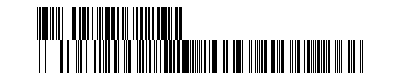

```mathematica
ArrayPlot[{btest,keystream}]
```

```mathematica
IntegerDigits[FromDigits[TriviumKeystream[key,IV,64,1151],2],16]
```

{2,9,8,0,0,0,0,7,8,0,0,0,0,0,0,0,0,0,2,12,11,3,12,0,0,0,1,14,9,8,0,0,0,0,5,9,6,0,14,14,0,0,0,7,10,1,0,2,6,8,10,6,9,2,5,13,2,5,11,9,13,9,5,5,13,1,3,10,14,8,8,13,1,0,8,1,0,12,11,4,11,15,13,7,4,2,2,12,2,2,5,14,7,1,12,0,14,8,4,13,8,9,4,12,9,8,3,0,7,4,12,2,7,15,11,4,14,10,14,0,12,10,2,2,11,6,11,1,10,11,3,14,7,12,3,14,3,13,8,10,8,6,0,10,3,6,5,6,5,9,4,7,6,8,11,13,15,13,12,0,4,8,1,2,7,12,3,11,5,5,10,11,7,15,12,11,10,4,5,8,5,2,12,9,4,9,0,10,3,14,1,13,14,10,15,3,8,14,2,8,15,14,14,6,0,13,11,4,14,14,6,1,0,7,11,14,14,14,12,12,4,0,10,4,7,10,0,14,12,5,13,9,4,4,8,3,11,0,13,15,8,15,12,15,10,5,7,11,11,12,14,9,4,15,7,4,11,6,9,11,1,2,7,10,15,4,6,8,8,6,2,4,8,11,5,12,5,8,3,2,4,9,3,5,5,6,6,12}